```mathematica
(* Constrain other cosmological parameter by real eta_tot = N^{\pm 1} imaginary eta_tot*)
```

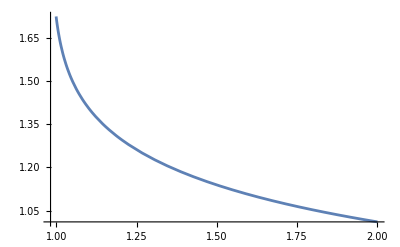

```mathematica
(* Closed, kappa > 0, 4 real roots: 2 kt^3/mt^2 > gp(x) > gm(x) *)
(* In this case, there is a contour satisfying Witten's criterion. *)

Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm]
r=lam=1;
x=(k r)/m^2;
gp[x]=((1+8 x)+(1+8/3 x)√(1+32/3 x))/(1+3 √(1+32/3 x));
gm[x]=((1+8 x)-(1+8/3 x)√(1+32/3 x))/(1-3 √(1+32/3 x));
kt=k/lam;
mt=m/lam;
rt=r/lam;
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));

Reη = 2 EllipticK[mm]/rho;
Imη = 2 EllipticK[1-mm]/rho;
Devide =Reη/Imη;
Plot[Devide/.{m->1},{k,0,2},PlotRange->{Automatic,Automatic}]
```

(ⅇ^(A/lam) lam (A+lam)-A^2 ExpIntegralEi[A/lam])/(2 (ⅇ^(A/lam) lam-A ExpIntegralEi[A/lam]))

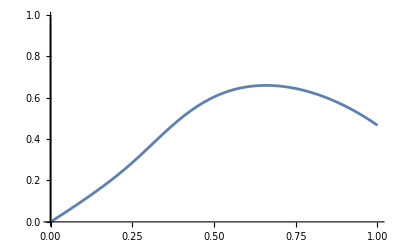

```mathematica
expecLam=Integrate[lam Exp[A/lam],lam]/ Integrate[Exp[ A/lam],lam]
Plot[expecLam/.{A->3}, {lam,0,1}]
```